## Árboles

```mathematica
<<VilCretas`
```

```mathematica
-Graphics-
(* Cuando todos los padres tienen k hijos, a ese árbol se le llama binario completo *)
(* Cuando el árbol es de orden k=2, se le denomia árbol binario *)
```

```mathematica
-Graphics-
(* La altura hace referencia al nivel de profundidad *)
(* Las hojas son los nodos que no son padres *)
(* Lo árboles balanceados tienen la ventaja de ser más rápido realizar una búsqueda, o recorrerlo *)
```

```mathematica
(*  El orden de los árboles lo da la cantidad máxima de hijos que tiene un padre *)
```

```mathematica
(* Orden: cantidad maxima de hijos que tiene un padre: 6 *)
(* Numero de nodos terminales (hojas): 13  *)
(* Altura (contar los niveles menos el padre): 5   *)
(* Arbol completo? Para ser completo todos los padres deben de tener el mismo numero de hijos: Falso *)
(* Arbol balanceado? Todas las hojas se encuentran en el nivel h o h-1 y ademas todas los padres tienen el mismo numero de hijos, menos en el nivel h-1 *)
(* Nodos en el nivel 2, se empiezan a contar despues del padre: 4 *)
```

```mathematica
(* (a) Es binario, porque los hijos tienen dos hijos *)
(* Los ultimos hijos son las hojas *)
(* Las alturas se empiezan a contar despues del nodo raiz, o sea despues del primero nodo, la altura de, primer arbol es 3 y del segundo es 4 *)
(* Importante: Para que un grafo sea un arbol debe de ser conexo y no tener cicuitos *)
```

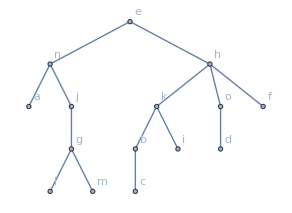

```mathematica
Arbol[{{e,n},{e,h},{n,a},{n,j},{h,k},{h,o},{h,f},{j,g},{k,b},{k,i},{o,d},{g,l},{g,m},{b,c}}]
```

```mathematica
(* Para cambiar el nodo raiz del arbol, al final se pone el nodo raiz que se quiere *)
```

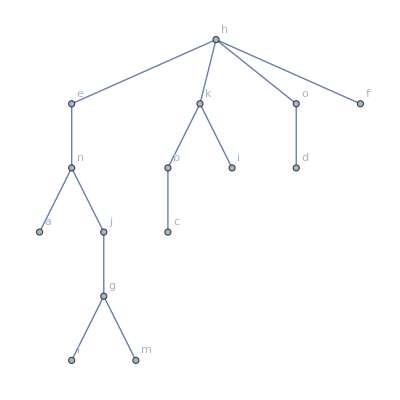

```mathematica
ar=ArbolR[{{e,n},{e,h},{n,a},{n,j},{h,k},{h,o},{h,f},{j,g},{k,b},{k,i},{o,d},{g,l},{g,m},{b,c}},h]
```

```mathematica
(* Muestra la altura del arbol, se tiene que especificar la raiz *)
```

```mathematica
Altura[ar,h]
```

5

```mathematica
(* Muestra las hojas del arbol, importante poner raiz-> para que no se muestre como una hoja en caso de tener valencia 1 *)
```

```mathematica
Hojas[ar,raiz->h]
```

{a,c,d,f,i,l,m}

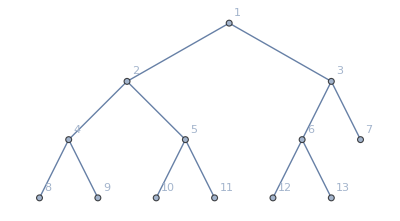

```mathematica
ArbolBinario[13]
```

```mathematica
(* En este caso, sí es un árbol binario completo, aunque el 7 no tenga hijos, la condición solo dice que es necesario que los nodos internos tengan dos hijos *)
```

```mathematica
gr=Grafo[{{e,n},{e,h},{n,a},{n,j},{h,k},{h,o},{h,f},{j,g},{k,b},{k,i},{o,d},{g,l},{g,m},{b,c}}];
```

```mathematica
ArbolJQ[gr]
```

True

```mathematica
(*--------------------------------------------------------------------------------------------*)
```

```mathematica
(* Se puede representar como un arbol binario, en cada nodo se tiene dos opciones, moverse a la derecha o hacia arriba, hasta terminar *)
```

```mathematica
(* Se empieza en 1, y asi va sucecivamente, con 4 etc *)
```

```mathematica
(* Al final lo que se pregunta, es la cantidad de rutas, o sea la cantidad de hojas que tiene el arbol *)
```

```mathematica
(* La cantidad de hojas seria 20, o sea la cantidad de rutas diferentes posibles *)
```

```mathematica
(*------------------------------------------------------------------------------------------*)
```

## Algoritmo de Huffman optimizado y no optimizado

```mathematica
(* Algoritmo de Huffman no optimizado, para codificar la palabra enrique *)
```

```mathematica
(* Es no optimizado porque probablemente no va a quedar balanceado *)
```

```mathematica
(* Ambos arboles resultantes, ya sean optimixados o no, son arboles binarios completos *)
```

```mathematica
(* Comando ArbolHuffmanN El primero no lo hace optimizado, el segundo si *)
```

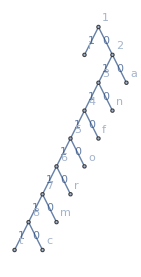
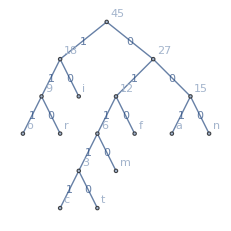

```mathematica
{ArbolHuffmanN["informatica"],ArbolHuffman["informatica"]}
```

```mathematica
(* Con frecuencias se puede ver el número de frecuencias asignadas *)
```

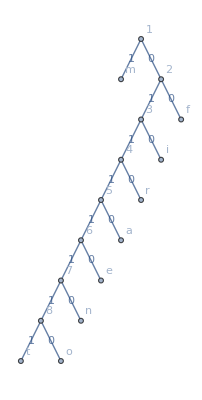

```mathematica
ArbolHuffmanN["firmamento"]
```

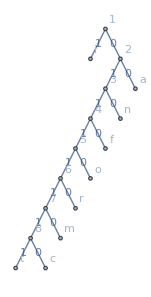
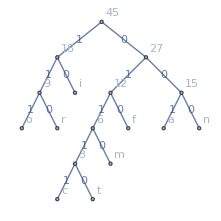
{{{{i,2},{a,2},{n,1},{f,1},{o,1},{r,1},{m,1},{t,1},{c,1}},-Graphics-},{{{c,1},{t,2},{m,3},{r,4},{o,5},{f,6},{n,7},{a,8},{i,9}},-Graphics-}}

```mathematica
{ArbolHuffmanN["informatica",frecuencias->True],ArbolHuffman["informatica",frecuencias->True]}
```

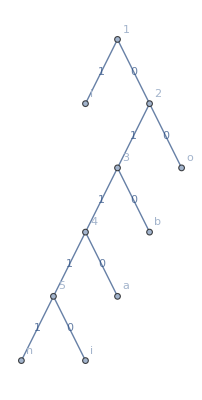
{1011100111100,-Graphics-}

```mathematica
HileraArbolHuffman["lino","lobanillo", tree->True]
```

```mathematica
(*------------------------------------------------------------------------------------------*)
```

```mathematica
(* El objetivo es representar la expresion de afuera hacia adentro *)
```

Plus[Times[-1, Plus[a, b], c], Times[Plus[Times[Plus[a, b], c], d], e], Times[-1, f]]

{1→Plus,2→Times,3→-1,4→Plus,5→a,6→b,7→c,8→Times,9→Plus,10→Times,11→Plus,12→a,13→b,14→c,15→d,16→e,17→Times,18→-1,19→f}

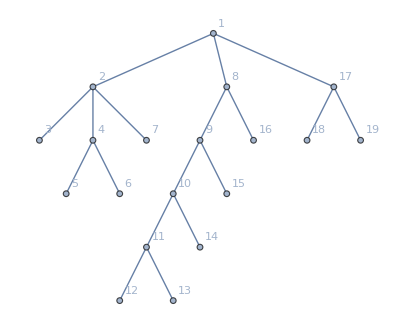

```mathematica
ArbolExpAlgebraica[(((a+b) c+d) e)-((a+b) c+f)]
```

```mathematica
(* Las hojas del arbol siempre tiene que ser las letras o numeros si trajera numeros en vez de letras *)
```

```mathematica
(*---------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------*)
```

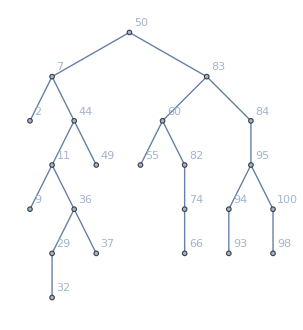

```mathematica
ArbolBinarioBusqueda[{50,7,44,83,84,2,11,95,36,60,94,29,37,100,82,55,9,32,93,74,49,98,66}]
```

```mathematica
(*--------------------------------------------------------------------------------------*)
```

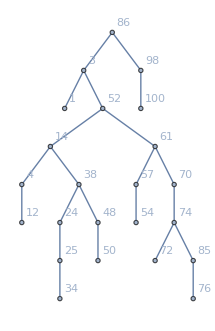

```mathematica
ArbolBinarioBusqueda[{86,3,52,98,14,38,24,1,61,48,57,25,70,34,74,72,85,76,50,54,100,4,12}]
```

```mathematica
(* Si se pone direction true, muestra la arista del hijo con direccion, recordar que hacia la izquiera es cuando es menor y hacia la derecha es cuando es mayor *)
```

```mathematica
ArbolBinarioBusqueda[{86,3,52,98,14,38,24,1,61,48,57,25,70,34,74,72,85,76,50,54,100,4,12},direction->True]
```

-Graphics-

```mathematica
(*----------------------------------------------------------------------*)
```

```mathematica
(* cuando hay caracteres para utilizar un arbol binario de busqueda se usa la posicion de los caracteres en el abecedario *)
```

```mathematica
(* 27 -> son 27 letras en el abecedario en espa;ol *)
(* Thread muestra la posicion de cada letra *)
```

```mathematica
Thread[Alphabet["Spanish"]->Range[27]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,ñ→15,o→16,p→17,q→18,r→19,s→20,t→21,u→22,v→23,w→24,x→25,y→26,z→27}

```mathematica
(* Las letras son caracteres entonces se convierten a string con el comando toString *)
```

```mathematica
ToString/@{p,e,y,k,c,t,b,j,u,f,i,d,m,x,l,v,n,a,g}/.
Thread[Alphabet["Spanish"]->Range[27]]
```

{17,5,26,11,3,21,2,10,22,6,9,4,13,25,12,23,14,1,7}

```mathematica
(* Igualmente, el comando corre aunque sean caracteres: *)
```

```mathematica
{ArbolBinarioBusqueda[{17,5,26,11,3,21,2,10,22,6,9,4,13,25,12,23,14,1,7},direction->True],ArbolBinarioBusqueda[{p,e,y,k,c,t,b,j,u,f,i,d,m,x,l,v,n,a,g},direction->True]}
```

{-Graphics-,-Graphics-}

```mathematica
(*----------------------------------------------------------------------*)
```

```mathematica
(* Posiciones de las letras: *)
```

```mathematica
{"a"->1,"b"->2,"c"->3,"d"->4,"e"->5,"f"->6,"g"->7,"h"->8,"i"->9,"j"->10,"k"->11,"l"->12,"m"->13,"n"->14,"ñ"->15,"o"->16,"p"->17,"q"->18,"r"->19,"s"->20,"t"->21,"u"->22,"v"->23,"w"->24,"x"->25,"y"->26,"z"->27}
```

```mathematica
(* Se van comparando las posiciones en el abecedario de la letra incial de cada palabra y se va armando el arbol*)
(* Si las letras son iguales, se compara con la siguiente letra y asi sucesivamente hasta que una sea mayor *)
```

```mathematica
(* Igualmente el comando ArbolBinarioBusqueda funciona con strings*)
```

```mathematica
arbol=ArbolBinarioBusqueda["el universo no se comporta de acuerdo con nuestras ideas preconcebidas",direction->True]
```

-Graphics-

```mathematica
Postfijo[arbol,"el"]
```

{acuerdo,con,de,comporta,ideas,preconcebidas,nuestras,se,no,universo,el}

## Recorridos en un Árbol

```mathematica
(* Su objetivo es encontrar un dato, siempre y cuando el arbol sea un arbol binario *)
```

```mathematica
(* Las posiciones del nodo raiz quedan al principio, si es de orden inicial, en el medio si es orden intermedio y al final si es orden final *)
```

```mathematica
(*---------------------------------------------------------------------*)
```

```mathematica
(* orden inicial *)
```

```mathematica
(* abhiklmjcdefngo *)
```

```mathematica
(* orden intermedio *)
```

```mathematica
(* ilkmhjbadnfegoc *)

(* orden fianl *)
(* lmkijhbnfogedca *)
```

```mathematica
(* Otro ejemplo: *)
A=ArbolBinarioBusqueda[{96,24,65,97,87,84,66,94,44,33,9,36,17,67,11},direction->True]
```

-Graphics-

```mathematica
Postfijo[A,96]
```

{11,17,9,36,33,44,67,66,84,94,87,65,24,97,96}

```mathematica
(* Interfijo *)
(* 9,11,17,24,33,36,44,65,66,57,84,87,94,96,97 *)
```

## Notaciones

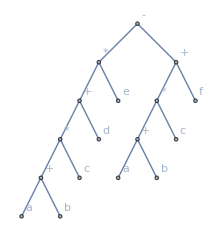

```mathematica
(* En la notacion polaca primero aparece la opercion y luego los operandos *)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(* Recorrer el arbol con orden inicial para hallar la notacion polaca: *)
```

```mathematica
(* Y quedaria: ++-3*2a/*c-f4g+a-/b*2c-*3de   *)
```

```mathematica
(* Ahora, para hallar la notacion polaca inversa, recorrer el arbol con orden final: *)
```

```mathematica
(* Y quedaria: 32a*-cf4-*g/+ab2c*/3d*e--++  *)
```

## Árboles Generadores

```mathematica
(* Los arboles generadores son los que contienen todos los nodos de un grafo conexo *)
```

## Buscar a lo ancho:

```mathematica
(* Permite construir un arbol de expansion, o sea un arbol que contiene todos los nodos de un grafo conexo, por niveles *)
```

```mathematica
(* Aca se agregan todas las aristas posibles *)
```

## Buscar a lo largo:

```mathematica
(* En esta se va agregando solo una arista, la menor *)
```

```mathematica
(*----------------------------------------------------------------------*)
```

```mathematica
(* Se finaliza cuando se tenga n-1 aristas, en este caso se va a finalizar cuando se tengan 7 aristas, ya que se tienen 8 nodos *)
```

```mathematica
(* Con el BPA se añaden todas las posibles aristas con cada nodo, iniciando donde dice la lista del orden de los nodos, luego se pasa al segundo nodo de la siguiente arista, se agregan las aristas que NO cierren circuitos *)

(* Luego con el BPL, se inicia igual en el nodo donde inicia la lista, y se agrega la arista 'menor', o sea la mas cercana a la letra con la que inicia el orden de los nodos, luego se pasa al segundo nodo de la siguiente arista, igual no se puede considerar las aristas que vayan a cerrar circuitos *)
```

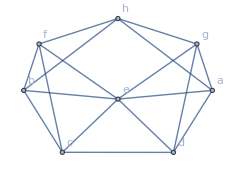

```mathematica
grafo=Grafo[{{a,d},{a,e},{a,g},{a,h},{b,e},{b,f},{c,d},{c,e},{d,e},{d,g},{e,f},{g,h},{g,e},{b,c},{f,h},{h,b},{f,c}}]
```

```mathematica
BuscarPrimeroAncho[grafo,orden->ListaVertices[grafo]]
```

{{a,d},{a,e},{a,g},{a,h},{c,d},{b,e},{e,f}}

```mathematica
BuscarPrimeroLargo[grafo,orden->ListaVertices[grafo]]
```

{{a,d},{c,d},{b,c},{b,e},{e,f},{f,h},{g,h}}

```mathematica
(* Se puede ver una animacion del comando: *)
```

```mathematica
BuscarPrimeroAncho[grafo,orden->ListaVertices[grafo],animacion->True]
```

{{a,d},{a,e},{a,g},{a,h},{c,d},{b,e},{e,f}}

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
(*----------------------------------------------------------------------------------*)
```

```mathematica
(* Recordar: siempre se parte del calculo de n-1, en este caso, n=10, o sea el total de aristas buscadas serian 9 *)
```

```mathematica
(* En el caso del BPL, se queda en e,f y ya no se puede ahregar nada mas porque se crearia un circuito,  hay que devolverse a su padre para poder seguir encontrando otras aristas *)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(*  orden -> {k, i, l, j, a, c, h, f, d, b, e, g}  *)
```

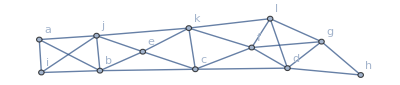

```mathematica
grafo=Grafo[{{a,b},{a,j},{b,i},{b,c},{b,e},{b,j},{c,d},{c,e},{c,f},{c,k},{d,f},{d,l},{d,g},{e,j},{e,k},{f,k},{f,l},{g,l},{g,h},{g,f},{j,i},{j,k},{k,l},{a,i},{d,h}}]
```

```mathematica
BuscarPrimeroAncho[grafo,orden->{k,i,l,j,a,c,h,f,d,b,e,g}]
```

{{k,l},{k,j},{k,c},{k,f},{k,e},{l,d},{l,g},{i,j},{j,a},{j,b},{h,d}}

```mathematica
BuscarPrimeroLargo[grafo,orden->{k,i,l,j,a,c,h,f,d,b,e,g}]
```

{{k,l},{l,f},{c,f},{c,d},{h,d},{h,g},{c,b},{i,b},{i,j},{j,a},{j,e}}

## Árboles de expansión mínima

# Algoritmo de Prim

```mathematica
(* El arbol que sera creado siempre va a ser UNICO *)
(* La suma de los pesos de las aristas resultantes en el arbol sera siempre el valor minimo *)
```

# Algoritmo de Kruskal

```mathematica
(*---------------------------------------------------------------------------------*)
```

```mathematica
(* Prim: *)
```

```mathematica
(* Kruskal: *)
```

```mathematica
(* En este no interesa el orden de los nodos *)
```

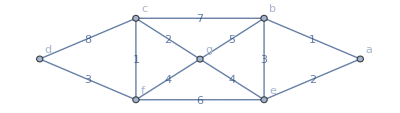

```mathematica
grafo=Grafo[{{a,b},{a,e},{b,c},{b,e},{b,g},{c,d},{c,f},{c,g},{d,f},{e,f},{e,g},{f,g}},pesos->{1,2,7,3,5,8,1,2,3,6,4,4},mostrarpesos->True]
```

```mathematica
Prim[grafo,orden->ListaVertices[grafo]]
```

El orden de los nodos es: {a,b,c,d,e,f,g}

T={{a,b},{a,e},{e,g},{g,c},{c,f},{f,d}}

Peso: 13

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
Kruskal[grafo]
```

T={a<->b,c<->f,c<->g,a<->e,d<->f,e<->g}

Peso: 13

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
(*-------------------------------------------------------------------------*)
```

Ejemplo 6.21: orden → {a, b, c, d, e, f, g, h}

```mathematica
(* n-1 = 7 *)
```

```mathematica
(* Como e,f y e,c son iguales, entonces se compara primero las primeras letras, e, pero como son iguales, se comparan las segundas, f y c, entonces se agrega e,c y asi con c,g y e,f *)
```

```mathematica
(* Prim: *)
```

```mathematica
(* Kruskal: *)
```

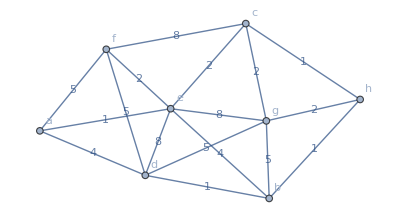

```mathematica
grafo=Grafo[{{a,d},{a,f},{d,b},{g,c},{d,f},{d,g},{e,b},{e,c},{e,d},{e,f},{e,g},{f,c},{g,b},{h,c},{h,g},{a,e},{b,h}},pesos->{4,5,1,2,5,5,4,2,8,2,8,8,5,1,2,1,1},mostrarpesos->True]
```

```mathematica
Prim[grafo,orden->ListaVertices[grafo]]
```

El orden de los nodos es: {a,b,c,d,e,f,g,h}

T={{a,e},{e,c},{c,h},{h,b},{b,d},{c,g},{e,f}}

Peso: 10

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
(* Para ver todas las iteraciones: *)
```

```mathematica
Prim[grafo,orden->ListaVertices[grafo],all->True]
```

Tabla de pesos del grafo:

| a | b | c | d | e | f | g | h
a | 0 | 0 | 0 | 4 | 1 | 5 | 0 | 0
b | 0 | 0 | 0 | 1 | 4 | 0 | 5 | 1
c | 0 | 0 | 0 | 0 | 2 | 8 | 2 | 1
d | 4 | 1 | 0 | 0 | 8 | 5 | 5 | 0
e | 1 | 4 | 2 | 8 | 0 | 2 | 8 | 0
f | 5 | 0 | 8 | 5 | 2 | 0 | 0 | 0
g | 0 | 5 | 2 | 5 | 8 | 0 | 0 | 2
h | 0 | 1 | 1 | 0 | 0 | 0 | 2 | 0

El orden de los nodos es: {a,b,c,d,e,f,g,h}

*** Inicialización ***

Aristas seleccionables (AS) del árbol T a construir: {{{a,d},4},{{a,e},1},{{a,f},5}}

*** Iteración 1 ***

Se agregó la arista: {a,e}, T={{a,e}}

Peso mínimo acumulado: 1

AS={{{a,d},4},{{a,f},5},{{e,b},4},{{e,c},2},{{e,d},8},{{e,f},2},{{e,g},8}}

*** Iteración 2 ***

Se agregó la arista: {e,c}, T={{a,e},{e,c}}

Peso mínimo acumulado: 3

AS={{{a,d},4},{{a,f},5},{{e,b},4},{{e,d},8},{{e,f},2},{{e,g},8},{{c,f},8},{{c,g},2},{{c,h},1}}

*** Iteración 3 ***

Se agregó la arista: {c,h}, T={{a,e},{e,c},{c,h}}

Peso mínimo acumulado: 4

AS={{{a,d},4},{{a,f},5},{{e,b},4},{{e,d},8},{{e,f},2},{{e,g},8},{{c,f},8},{{c,g},2},{{h,b},1},{{h,g},2}}

*** Iteración 4 ***

Se agregó la arista: {h,b}, T={{a,e},{e,c},{c,h},{h,b}}

Peso mínimo acumulado: 5

AS={{{a,d},4},{{a,f},5},{{e,d},8},{{e,f},2},{{e,g},8},{{c,f},8},{{c,g},2},{{h,g},2},{{b,d},1},{{b,g},5}}

*** Iteración 5 ***

Se agregó la arista: {b,d}, T={{a,e},{e,c},{c,h},{h,b},{b,d}}

Peso mínimo acumulado: 6

AS={{{a,f},5},{{e,f},2},{{e,g},8},{{c,f},8},{{c,g},2},{{h,g},2},{{b,g},5},{{d,f},5},{{d,g},5}}

*** Iteración 6 ***

Se agregó la arista: {c,g}, T={{a,e},{e,c},{c,h},{h,b},{b,d},{c,g}}

Peso mínimo acumulado: 8

AS={{{a,f},5},{{e,f},2},{{c,f},8},{{d,f},5}}

*** Iteración 7 ***

Se agregó la arista: {e,f}, T={{a,e},{e,c},{c,h},{h,b},{b,d},{c,g},{e,f}}

Peso mínimo acumulado: 10

AS={}

*** Finalmente ***

T={{a,e},{e,c},{c,h},{h,b},{b,d},{c,g},{e,f}}

Peso: 10

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
Kruskal[grafo]
```

T={b<->h,a<->e,h<->c,d<->b,g<->c,e<->f,e<->c}

Peso: 10

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
(*--------------------------------------------------------------------------------*)
```

```mathematica
(* Para encontrar un arbol de expasion maxima, se multiplican los pesos por un -1, y se le aplica el valor absoluto al final *)
```

```mathematica
grafo=Grafo[{{h,f},{a,f},{a,g},{a,h},{a,i},{b,e},{b,f},{b,g},{b,h},{b,i},{c,e},{c,f},{c,g},{c,h},{e,i},{d,e},{d,g},{d,i},{h,g}},pesos->-1{2,2,7,1,4,4,2,2,9,8,8,2,7,8,3,2,7,7,5},mostrarpesos->True];
```

```mathematica
Prim[grafo,orden->{d, e, f, c, a, i, h, g, b}]
```

El orden de los nodos es: {d,e,f,c,a,i,h,g,b}

T={{d,i},{i,b},{b,h},{h,c},{c,e},{d,g},{g,a},{c,f}}

Peso: -56

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
Kruskal[grafo]
```

T={b<->h,c<->h,c<->e,b<->i,a<->g,d<->g,d<->i,c<->f}

Peso: -56

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.